```mathematica
ConvertList[str_]:=ToExpression[StringReplace[str,{"["->"{","]"->"}"}]]
```

```mathematica
StringReplace["[[0,1],[0,2],[0,3],[0,4],[1,2],[1,4],[2,3],[3,4]]",{"["->"{","]"->"}"}]
```

```mathematica
Sort[Map[Sort,{{0,1},{0,2},{1,2},{11,13},{12,13},{3,1},{4,2},{5,3},{6,4},{7,5},{8,6},{9,7},{10,8},{11,9},{12,10},{3,4},{5,6},{7,8},{9,10},{11,12}}]]
```

{{0,1},{0,2},{1,2},{1,3},{2,4},{3,4},{3,5},{4,6},{5,6},{5,7},{6,8},{7,8},{7,9},{8,10},{9,10},{9,11},{10,12},{11,12},{11,13},{12,13}}

```mathematica
Map[First[#]<->Last[#]&, {{0,1},{0,2},{0,3},{0,4},{1,2},{1,4},{2,3},{3,4}}]
```

```mathematica
Graph[{0<->1,0<->2,0<->3,0<->4,1<->2,1<->4,2<->3,3<->4},VertexLabels->"Name"]
```

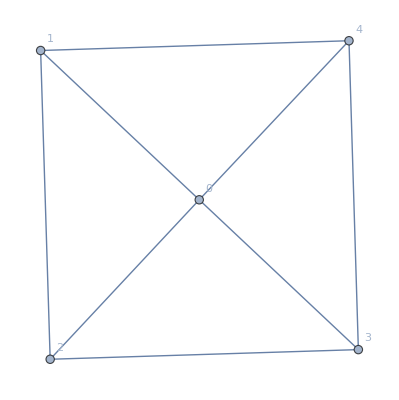
```mathematica
LineGraph[-Graphics-]
```

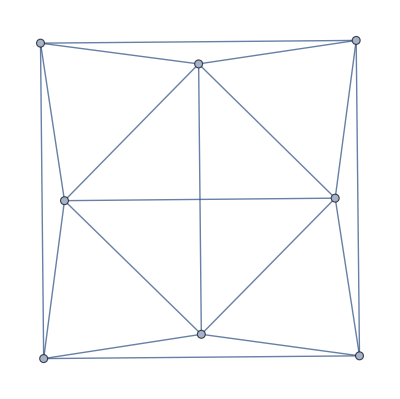
```mathematica
Map[Length,FindCycle[-Graphics-,∞,All]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
ls=ToExpression[StringReplace["[[0,1,2],[0,1,2,3],[0,1,2,4,5,3],[0,1,2,4,5,6,3],[0,1,2,4,5,7,8,6,3],[0,1,2,4,5,7,8,9,6,3],[0,1,2,4,5,7,8,10,11,9,6,3],[0,1,2,4,5,7,8,10,11,12,9,6,3],[0,1,2,4,5,7,8,10,11,13,12,9,6,3],[0,1,2,4,5,7,8,10,13,11,9,6,3],[0,1,2,4,5,7,8,10,13,11,12,9,6,3],[0,1,2,4,5,7,8,10,13,12,9,6,3],[0,1,2,4,5,7,8,10,13,12,11,9,6,3],[0,1,2,4,5,7,10,8,6,3],[0,1,2,4,5,7,10,8,9,6,3],[0,1,2,4,5,7,10,11,9,6,3],[0,1,2,4,5,7,10,11,9,8,6,3],[0,1,2,4,5,7,10,11,12,9,6,3],[0,1,2,4,5,7,10,11,12,9,8,6,3],[0,1,2,4,5,7,10,11,13,12,9,6,3],[0,1,2,4,5,7,10,11,13,12,9,8,6,3],[0,1,2,4,5,7,10,13,11,9,6,3],[0,1,2,4,5,7,10,13,11,9,8,6,3],[0,1,2,4,5,7,10,13,11,12,9,6,3],[0,1,2,4,5,7,10,13,11,12,9,8,6,3],[0,1,2,4,5,7,10,13,12,9,6,3],[0,1,2,4,5,7,10,13,12,9,8,6,3],[0,1,2,4,5,7,10,13,12,11,9,6,3],[0,1,2,4,5,7,10,13,12,11,9,8,6,3],[0,1,2,4,7,5,3],[0,1,2,4,7,5,6,3],[0,1,2,4,7,8,6,3],[0,1,2,4,7,8,6,5,3],[0,1,2,4,7,8,9,6,3],[0,1,2,4,7,8,9,6,5,3],[0,1,2,4,7,8,10,11,9,6,3],[0,1,2,4,7,8,10,11,9,6,5,3],[0,1,2,4,7,8,10,11,12,9,6,3],[0,1,2,4,7,8,10,11,12,9,6,5,3],[0,1,2,4,7,8,10,11,13,12,9,6,3],[0,1,2,4,7,8,10,11,13,12,9,6,5,3],[0,1,2,4,7,8,10,13,11,9,6,3],[0,1,2,4,7,8,10,13,11,9,6,5,3],[0,1,2,4,7,8,10,13,11,12,9,6,3],[0,1,2,4,7,8,10,13,11,12,9,6,5,3],[0,1,2,4,7,8,10,13,12,9,6,3],[0,1,2,4,7,8,10,13,12,9,6,5,3],[0,1,2,4,7,8,10,13,12,11,9,6,3],[0,1,2,4,7,8,10,13,12,11,9,6,5,3],[0,1,2,4,7,10,8,6,3],[0,1,2,4,7,10,8,6,5,3],[0,1,2,4,7,10,8,9,6,3],[0,1,2,4,7,10,8,9,6,5,3],[0,1,2,4,7,10,11,9,6,3],[0,1,2,4,7,10,11,9,6,5,3],[0,1,2,4,7,10,11,9,8,6,3],[0,1,2,4,7,10,11,9,8,6,5,3],[0,1,2,4,7,10,11,12,9,6,3],[0,1,2,4,7,10,11,12,9,6,5,3],[0,1,2,4,7,10,11,12,9,8,6,3],[0,1,2,4,7,10,11,12,9,8,6,5,3],[0,1,2,4,7,10,11,13,12,9,6,3],[0,1,2,4,7,10,11,13,12,9,6,5,3],[0,1,2,4,7,10,11,13,12,9,8,6,3],[0,1,2,4,7,10,11,13,12,9,8,6,5,3],[0,1,2,4,7,10,13,11,9,6,3],[0,1,2,4,7,10,13,11,9,6,5,3],[0,1,2,4,7,10,13,11,9,8,6,3],[0,1,2,4,7,10,13,11,9,8,6,5,3],[0,1,2,4,7,10,13,11,12,9,6,3],[0,1,2,4,7,10,13,11,12,9,6,5,3],[0,1,2,4,7,10,13,11,12,9,8,6,3],[0,1,2,4,7,10,13,11,12,9,8,6,5,3],[0,1,2,4,7,10,13,12,9,6,3],[0,1,2,4,7,10,13,12,9,6,5,3],[0,1,2,4,7,10,13,12,9,8,6,3],[0,1,2,4,7,10,13,12,9,8,6,5,3],[0,1,2,4,7,10,13,12,11,9,6,3],[0,1,2,4,7,10,13,12,11,9,6,5,3],[0,1,2,4,7,10,13,12,11,9,8,6,3],[0,1,2,4,7,10,13,12,11,9,8,6,5,3],[0,1,4,2],[0,1,4,2,3],[0,1,4,5,3],[0,1,4,5,3,2],[0,1,4,5,6,3],[0,1,4,5,6,3,2],[0,1,4,5,7,8,6,3],[0,1,4,5,7,8,6,3,2],[0,1,4,5,7,8,9,6,3],[0,1,4,5,7,8,9,6,3,2],[0,1,4,5,7,8,10,11,9,6,3],[0,1,4,5,7,8,10,11,9,6,3,2],[0,1,4,5,7,8,10,11,12,9,6,3],[0,1,4,5,7,8,10,11,12,9,6,3,2],[0,1,4,5,7,8,10,11,13,12,9,6,3],[0,1,4,5,7,8,10,11,13,12,9,6,3,2],[0,1,4,5,7,8,10,13,11,9,6,3],[0,1,4,5,7,8,10,13,11,9,6,3,2],[0,1,4,5,7,8,10,13,11,12,9,6,3],[0,1,4,5,7,8,10,13,11,12,9,6,3,2],[0,1,4,5,7,8,10,13,12,9,6,3],[0,1,4,5,7,8,10,13,12,9,6,3,2],[0,1,4,5,7,8,10,13,12,11,9,6,3],[0,1,4,5,7,8,10,13,12,11,9,6,3,2],[0,1,4,5,7,10,8,6,3],[0,1,4,5,7,10,8,6,3,2],[0,1,4,5,7,10,8,9,6,3],[0,1,4,5,7,10,8,9,6,3,2],[0,1,4,5,7,10,11,9,6,3],[0,1,4,5,7,10,11,9,6,3,2],[0,1,4,5,7,10,11,9,8,6,3],[0,1,4,5,7,10,11,9,8,6,3,2],[0,1,4,5,7,10,11,12,9,6,3],[0,1,4,5,7,10,11,12,9,6,3,2],[0,1,4,5,7,10,11,12,9,8,6,3],[0,1,4,5,7,10,11,12,9,8,6,3,2],[0,1,4,5,7,10,11,13,12,9,6,3],[0,1,4,5,7,10,11,13,12,9,6,3,2],[0,1,4,5,7,10,11,13,12,9,8,6,3],[0,1,4,5,7,10,11,13,12,9,8,6,3,2],[0,1,4,5,7,10,13,11,9,6,3],[0,1,4,5,7,10,13,11,9,6,3,2],[0,1,4,5,7,10,13,11,9,8,6,3],[0,1,4,5,7,10,13,11,9,8,6,3,2],[0,1,4,5,7,10,13,11,12,9,6,3],[0,1,4,5,7,10,13,11,12,9,6,3,2],[0,1,4,5,7,10,13,11,12,9,8,6,3],[0,1,4,5,7,10,13,11,12,9,8,6,3,2],[0,1,4,5,7,10,13,12,9,6,3],[0,1,4,5,7,10,13,12,9,6,3,2],[0,1,4,5,7,10,13,12,9,8,6,3],[0,1,4,5,7,10,13,12,9,8,6,3,2],[0,1,4,5,7,10,13,12,11,9,6,3],[0,1,4,5,7,10,13,12,11,9,6,3,2],[0,1,4,5,7,10,13,12,11,9,8,6,3],[0,1,4,5,7,10,13,12,11,9,8,6,3,2],[0,1,4,7,5,3],[0,1,4,7,5,3,2],[0,1,4,7,5,6,3],[0,1,4,7,5,6,3,2],[0,1,4,7,8,6,3],[0,1,4,7,8,6,3,2],[0,1,4,7,8,6,5,3],[0,1,4,7,8,6,5,3,2],[0,1,4,7,8,9,6,3],[0,1,4,7,8,9,6,3,2],[0,1,4,7,8,9,6,5,3],[0,1,4,7,8,9,6,5,3,2],[0,1,4,7,8,10,11,9,6,3],[0,1,4,7,8,10,11,9,6,3,2],[0,1,4,7,8,10,11,9,6,5,3],[0,1,4,7,8,10,11,9,6,5,3,2],[0,1,4,7,8,10,11,12,9,6,3],[0,1,4,7,8,10,11,12,9,6,3,2],[0,1,4,7,8,10,11,12,9,6,5,3],[0,1,4,7,8,10,11,12,9,6,5,3,2],[0,1,4,7,8,10,11,13,12,9,6,3],[0,1,4,7,8,10,11,13,12,9,6,3,2],[0,1,4,7,8,10,11,13,12,9,6,5,3],[0,1,4,7,8,10,11,13,12,9,6,5,3,2],[0,1,4,7,8,10,13,11,9,6,3],[0,1,4,7,8,10,13,11,9,6,3,2],[0,1,4,7,8,10,13,11,9,6,5,3],[0,1,4,7,8,10,13,11,9,6,5,3,2],[0,1,4,7,8,10,13,11,12,9,6,3],[0,1,4,7,8,10,13,11,12,9,6,3,2],[0,1,4,7,8,10,13,11,12,9,6,5,3],[0,1,4,7,8,10,13,11,12,9,6,5,3,2],[0,1,4,7,8,10,13,12,9,6,3],[0,1,4,7,8,10,13,12,9,6,3,2],[0,1,4,7,8,10,13,12,9,6,5,3],[0,1,4,7,8,10,13,12,9,6,5,3,2],[0,1,4,7,8,10,13,12,11,9,6,3],[0,1,4,7,8,10,13,12,11,9,6,3,2],[0,1,4,7,8,10,13,12,11,9,6,5,3],[0,1,4,7,8,10,13,12,11,9,6,5,3,2],[0,1,4,7,10,8,6,3],[0,1,4,7,10,8,6,3,2],[0,1,4,7,10,8,6,5,3],[0,1,4,7,10,8,6,5,3,2],[0,1,4,7,10,8,9,6,3],[0,1,4,7,10,8,9,6,3,2],[0,1,4,7,10,8,9,6,5,3],[0,1,4,7,10,8,9,6,5,3,2],[0,1,4,7,10,11,9,6,3],[0,1,4,7,10,11,9,6,3,2],[0,1,4,7,10,11,9,6,5,3],[0,1,4,7,10,11,9,6,5,3,2],[0,1,4,7,10,11,9,8,6,3],[0,1,4,7,10,11,9,8,6,3,2],[0,1,4,7,10,11,9,8,6,5,3],[0,1,4,7,10,11,9,8,6,5,3,2],[0,1,4,7,10,11,12,9,6,3],[0,1,4,7,10,11,12,9,6,3,2],[0,1,4,7,10,11,12,9,6,5,3],[0,1,4,7,10,11,12,9,6,5,3,2],[0,1,4,7,10,11,12,9,8,6,3],[0,1,4,7,10,11,12,9,8,6,3,2],[0,1,4,7,10,11,12,9,8,6,5,3],[0,1,4,7,10,11,12,9,8,6,5,3,2],[0,1,4,7,10,11,13,12,9,6,3],[0,1,4,7,10,11,13,12,9,6,3,2],[0,1,4,7,10,11,13,12,9,6,5,3],[0,1,4,7,10,11,13,12,9,6,5,3,2],[0,1,4,7,10,11,13,12,9,8,6,3],[0,1,4,7,10,11,13,12,9,8,6,3,2],[0,1,4,7,10,11,13,12,9,8,6,5,3],[0,1,4,7,10,11,13,12,9,8,6,5,3,2],[0,1,4,7,10,13,11,9,6,3],[0,1,4,7,10,13,11,9,6,3,2],[0,1,4,7,10,13,11,9,6,5,3],[0,1,4,7,10,13,11,9,6,5,3,2],[0,1,4,7,10,13,11,9,8,6,3],[0,1,4,7,10,13,11,9,8,6,3,2],[0,1,4,7,10,13,11,9,8,6,5,3],[0,1,4,7,10,13,11,9,8,6,5,3,2],[0,1,4,7,10,13,11,12,9,6,3],[0,1,4,7,10,13,11,12,9,6,3,2],[0,1,4,7,10,13,11,12,9,6,5,3],[0,1,4,7,10,13,11,12,9,6,5,3,2],[0,1,4,7,10,13,11,12,9,8,6,3],[0,1,4,7,10,13,11,12,9,8,6,3,2],[0,1,4,7,10,13,11,12,9,8,6,5,3],[0,1,4,7,10,13,11,12,9,8,6,5,3,2],[0,1,4,7,10,13,12,9,6,3],[0,1,4,7,10,13,12,9,6,3,2],[0,1,4,7,10,13,12,9,6,5,3],[0,1,4,7,10,13,12,9,6,5,3,2],[0,1,4,7,10,13,12,9,8,6,3],[0,1,4,7,10,13,12,9,8,6,3,2],[0,1,4,7,10,13,12,9,8,6,5,3],[0,1,4,7,10,13,12,9,8,6,5,3,2],[0,1,4,7,10,13,12,11,9,6,3],[0,1,4,7,10,13,12,11,9,6,3,2],[0,1,4,7,10,13,12,11,9,6,5,3],[0,1,4,7,10,13,12,11,9,6,5,3,2],[0,1,4,7,10,13,12,11,9,8,6,3],[0,1,4,7,10,13,12,11,9,8,6,3,2],[0,1,4,7,10,13,12,11,9,8,6,5,3],[0,1,4,7,10,13,12,11,9,8,6,5,3,2],[0,2,1],[0,2,1,4,5,3],[0,2,1,4,5,6,3],[0,2,1,4,5,7,8,6,3],[0,2,1,4,5,7,8,9,6,3],[0,2,1,4,5,7,8,10,11,9,6,3],[0,2,1,4,5,7,8,10,11,12,9,6,3],[0,2,1,4,5,7,8,10,11,13,12,9,6,3],[0,2,1,4,5,7,8,10,13,11,9,6,3],[0,2,1,4,5,7,8,10,13,11,12,9,6,3],[0,2,1,4,5,7,8,10,13,12,9,6,3],[0,2,1,4,5,7,8,10,13,12,11,9,6,3],[0,2,1,4,5,7,10,8,6,3],[0,2,1,4,5,7,10,8,9,6,3],[0,2,1,4,5,7,10,11,9,6,3],[0,2,1,4,5,7,10,11,9,8,6,3],[0,2,1,4,5,7,10,11,12,9,6,3],[0,2,1,4,5,7,10,11,12,9,8,6,3],[0,2,1,4,5,7,10,11,13,12,9,6,3],[0,2,1,4,5,7,10,11,13,12,9,8,6,3],[0,2,1,4,5,7,10,13,11,9,6,3],[0,2,1,4,5,7,10,13,11,9,8,6,3],[0,2,1,4,5,7,10,13,11,12,9,6,3],[0,2,1,4,5,7,10,13,11,12,9,8,6,3],[0,2,1,4,5,7,10,13,12,9,6,3],[0,2,1,4,5,7,10,13,12,9,8,6,3],[0,2,1,4,5,7,10,13,12,11,9,6,3],[0,2,1,4,5,7,10,13,12,11,9,8,6,3],[0,2,1,4,7,5,3],[0,2,1,4,7,5,6,3],[0,2,1,4,7,8,6,3],[0,2,1,4,7,8,6,5,3],[0,2,1,4,7,8,9,6,3],[0,2,1,4,7,8,9,6,5,3],[0,2,1,4,7,8,10,11,9,6,3],[0,2,1,4,7,8,10,11,9,6,5,3],[0,2,1,4,7,8,10,11,12,9,6,3],[0,2,1,4,7,8,10,11,12,9,6,5,3],[0,2,1,4,7,8,10,11,13,12,9,6,3],[0,2,1,4,7,8,10,11,13,12,9,6,5,3],[0,2,1,4,7,8,10,13,11,9,6,3],[0,2,1,4,7,8,10,13,11,9,6,5,3],[0,2,1,4,7,8,10,13,11,12,9,6,3],[0,2,1,4,7,8,10,13,11,12,9,6,5,3],[0,2,1,4,7,8,10,13,12,9,6,3],[0,2,1,4,7,8,10,13,12,9,6,5,3],[0,2,1,4,7,8,10,13,12,11,9,6,3],[0,2,1,4,7,8,10,13,12,11,9,6,5,3],[0,2,1,4,7,10,8,6,3],[0,2,1,4,7,10,8,6,5,3],[0,2,1,4,7,10,8,9,6,3],[0,2,1,4,7,10,8,9,6,5,3],[0,2,1,4,7,10,11,9,6,3],[0,2,1,4,7,10,11,9,6,5,3],[0,2,1,4,7,10,11,9,8,6,3],[0,2,1,4,7,10,11,9,8,6,5,3],[0,2,1,4,7,10,11,12,9,6,3],[0,2,1,4,7,10,11,12,9,6,5,3],[0,2,1,4,7,10,11,12,9,8,6,3],[0,2,1,4,7,10,11,12,9,8,6,5,3],[0,2,1,4,7,10,11,13,12,9,6,3],[0,2,1,4,7,10,11,13,12,9,6,5,3],[0,2,1,4,7,10,11,13,12,9,8,6,3],[0,2,1,4,7,10,11,13,12,9,8,6,5,3],[0,2,1,4,7,10,13,11,9,6,3],[0,2,1,4,7,10,13,11,9,6,5,3],[0,2,1,4,7,10,13,11,9,8,6,3],[0,2,1,4,7,10,13,11,9,8,6,5,3],[0,2,1,4,7,10,13,11,12,9,6,3],[0,2,1,4,7,10,13,11,12,9,6,5,3],[0,2,1,4,7,10,13,11,12,9,8,6,3],[0,2,1,4,7,10,13,11,12,9,8,6,5,3],[0,2,1,4,7,10,13,12,9,6,3],[0,2,1,4,7,10,13,12,9,6,5,3],[0,2,1,4,7,10,13,12,9,8,6,3],[0,2,1,4,7,10,13,12,9,8,6,5,3],[0,2,1,4,7,10,13,12,11,9,6,3],[0,2,1,4,7,10,13,12,11,9,6,5,3],[0,2,1,4,7,10,13,12,11,9,8,6,3],[0,2,1,4,7,10,13,12,11,9,8,6,5,3],[0,2,3],[0,2,3,5,4,1],[0,2,3,5,6,8,7,4,1],[0,2,3,5,6,8,9,11,10,7,4,1],[0,2,3,5,6,8,9,11,12,13,10,7,4,1],[0,2,3,5,6,8,9,11,13,10,7,4,1],[0,2,3,5,6,8,9,12,11,10,7,4,1],[0,2,3,5,6,8,9,12,11,13,10,7,4,1],[0,2,3,5,6,8,9,12,13,10,7,4,1],[0,2,3,5,6,8,9,12,13,11,10,7,4,1],[0,2,3,5,6,8,10,7,4,1],[0,2,3,5,6,9,8,7,4,1],[0,2,3,5,6,9,8,10,7,4,1],[0,2,3,5,6,9,11,10,7,4,1],[0,2,3,5,6,9,11,10,8,7,4,1],[0,2,3,5,6,9,11,12,13,10,7,4,1],[0,2,3,5,6,9,11,12,13,10,8,7,4,1],[0,2,3,5,6,9,11,13,10,7,4,1],[0,2,3,5,6,9,11,13,10,8,7,4,1],[0,2,3,5,6,9,12,11,10,7,4,1],[0,2,3,5,6,9,12,11,10,8,7,4,1],[0,2,3,5,6,9,12,11,13,10,7,4,1],[0,2,3,5,6,9,12,11,13,10,8,7,4,1],[0,2,3,5,6,9,12,13,10,7,4,1],[0,2,3,5,6,9,12,13,10,8,7,4,1],[0,2,3,5,6,9,12,13,11,10,7,4,1],[0,2,3,5,6,9,12,13,11,10,8,7,4,1],[0,2,3,5,7,4,1],[0,2,3,6,5,4,1],[0,2,3,6,5,7,4,1],[0,2,3,6,8,7,4,1],[0,2,3,6,8,7,5,4,1],[0,2,3,6,8,9,11,10,7,4,1],[0,2,3,6,8,9,11,10,7,5,4,1],[0,2,3,6,8,9,11,12,13,10,7,4,1],[0,2,3,6,8,9,11,12,13,10,7,5,4,1],[0,2,3,6,8,9,11,13,10,7,4,1],[0,2,3,6,8,9,11,13,10,7,5,4,1],[0,2,3,6,8,9,12,11,10,7,4,1],[0,2,3,6,8,9,12,11,10,7,5,4,1],[0,2,3,6,8,9,12,11,13,10,7,4,1],[0,2,3,6,8,9,12,11,13,10,7,5,4,1],[0,2,3,6,8,9,12,13,10,7,4,1],[0,2,3,6,8,9,12,13,10,7,5,4,1],[0,2,3,6,8,9,12,13,11,10,7,4,1],[0,2,3,6,8,9,12,13,11,10,7,5,4,1],[0,2,3,6,8,10,7,4,1],[0,2,3,6,8,10,7,5,4,1],[0,2,3,6,9,8,7,4,1],[0,2,3,6,9,8,7,5,4,1],[0,2,3,6,9,8,10,7,4,1],[0,2,3,6,9,8,10,7,5,4,1],[0,2,3,6,9,11,10,7,4,1],[0,2,3,6,9,11,10,7,5,4,1],[0,2,3,6,9,11,10,8,7,4,1],[0,2,3,6,9,11,10,8,7,5,4,1],[0,2,3,6,9,11,12,13,10,7,4,1],[0,2,3,6,9,11,12,13,10,7,5,4,1],[0,2,3,6,9,11,12,13,10,8,7,4,1],[0,2,3,6,9,11,12,13,10,8,7,5,4,1],[0,2,3,6,9,11,13,10,7,4,1],[0,2,3,6,9,11,13,10,7,5,4,1],[0,2,3,6,9,11,13,10,8,7,4,1],[0,2,3,6,9,11,13,10,8,7,5,4,1],[0,2,3,6,9,12,11,10,7,4,1],[0,2,3,6,9,12,11,10,7,5,4,1],[0,2,3,6,9,12,11,10,8,7,4,1],[0,2,3,6,9,12,11,10,8,7,5,4,1],[0,2,3,6,9,12,11,13,10,7,4,1],[0,2,3,6,9,12,11,13,10,7,5,4,1],[0,2,3,6,9,12,11,13,10,8,7,4,1],[0,2,3,6,9,12,11,13,10,8,7,5,4,1],[0,2,3,6,9,12,13,10,7,4,1],[0,2,3,6,9,12,13,10,7,5,4,1],[0,2,3,6,9,12,13,10,8,7,4,1],[0,2,3,6,9,12,13,10,8,7,5,4,1],[0,2,3,6,9,12,13,11,10,7,4,1],[0,2,3,6,9,12,13,11,10,7,5,4,1],[0,2,3,6,9,12,13,11,10,8,7,4,1],[0,2,3,6,9,12,13,11,10,8,7,5,4,1],[0,2,4,1],[0,2,4,5,3],[0,2,4,5,6,3],[0,2,4,5,7,8,6,3],[0,2,4,5,7,8,9,6,3],[0,2,4,5,7,8,10,11,9,6,3],[0,2,4,5,7,8,10,11,12,9,6,3],[0,2,4,5,7,8,10,11,13,12,9,6,3],[0,2,4,5,7,8,10,13,11,9,6,3],[0,2,4,5,7,8,10,13,11,12,9,6,3],[0,2,4,5,7,8,10,13,12,9,6,3],[0,2,4,5,7,8,10,13,12,11,9,6,3],[0,2,4,5,7,10,8,6,3],[0,2,4,5,7,10,8,9,6,3],[0,2,4,5,7,10,11,9,6,3],[0,2,4,5,7,10,11,9,8,6,3],[0,2,4,5,7,10,11,12,9,6,3],[0,2,4,5,7,10,11,12,9,8,6,3],[0,2,4,5,7,10,11,13,12,9,6,3],[0,2,4,5,7,10,11,13,12,9,8,6,3],[0,2,4,5,7,10,13,11,9,6,3],[0,2,4,5,7,10,13,11,9,8,6,3],[0,2,4,5,7,10,13,11,12,9,6,3],[0,2,4,5,7,10,13,11,12,9,8,6,3],[0,2,4,5,7,10,13,12,9,6,3],[0,2,4,5,7,10,13,12,9,8,6,3],[0,2,4,5,7,10,13,12,11,9,6,3],[0,2,4,5,7,10,13,12,11,9,8,6,3],[0,2,4,7,5,3],[0,2,4,7,5,6,3],[0,2,4,7,8,6,3],[0,2,4,7,8,6,5,3],[0,2,4,7,8,9,6,3],[0,2,4,7,8,9,6,5,3],[0,2,4,7,8,10,11,9,6,3],[0,2,4,7,8,10,11,9,6,5,3],[0,2,4,7,8,10,11,12,9,6,3],[0,2,4,7,8,10,11,12,9,6,5,3],[0,2,4,7,8,10,11,13,12,9,6,3],[0,2,4,7,8,10,11,13,12,9,6,5,3],[0,2,4,7,8,10,13,11,9,6,3],[0,2,4,7,8,10,13,11,9,6,5,3],[0,2,4,7,8,10,13,11,12,9,6,3],[0,2,4,7,8,10,13,11,12,9,6,5,3],[0,2,4,7,8,10,13,12,9,6,3],[0,2,4,7,8,10,13,12,9,6,5,3],[0,2,4,7,8,10,13,12,11,9,6,3],[0,2,4,7,8,10,13,12,11,9,6,5,3],[0,2,4,7,10,8,6,3],[0,2,4,7,10,8,6,5,3],[0,2,4,7,10,8,9,6,3],[0,2,4,7,10,8,9,6,5,3],[0,2,4,7,10,11,9,6,3],[0,2,4,7,10,11,9,6,5,3],[0,2,4,7,10,11,9,8,6,3],[0,2,4,7,10,11,9,8,6,5,3],[0,2,4,7,10,11,12,9,6,3],[0,2,4,7,10,11,12,9,6,5,3],[0,2,4,7,10,11,12,9,8,6,3],[0,2,4,7,10,11,12,9,8,6,5,3],[0,2,4,7,10,11,13,12,9,6,3],[0,2,4,7,10,11,13,12,9,6,5,3],[0,2,4,7,10,11,13,12,9,8,6,3],[0,2,4,7,10,11,13,12,9,8,6,5,3],[0,2,4,7,10,13,11,9,6,3],[0,2,4,7,10,13,11,9,6,5,3],[0,2,4,7,10,13,11,9,8,6,3],[0,2,4,7,10,13,11,9,8,6,5,3],[0,2,4,7,10,13,11,12,9,6,3],[0,2,4,7,10,13,11,12,9,6,5,3],[0,2,4,7,10,13,11,12,9,8,6,3],[0,2,4,7,10,13,11,12,9,8,6,5,3],[0,2,4,7,10,13,12,9,6,3],[0,2,4,7,10,13,12,9,6,5,3],[0,2,4,7,10,13,12,9,8,6,3],[0,2,4,7,10,13,12,9,8,6,5,3],[0,2,4,7,10,13,12,11,9,6,3],[0,2,4,7,10,13,12,11,9,6,5,3],[0,2,4,7,10,13,12,11,9,8,6,3],[0,2,4,7,10,13,12,11,9,8,6,5,3],[0,3,2],[0,3,2,1],[0,3,2,4,1],[0,3,5,4,1],[0,3,5,4,1,2],[0,3,5,4,2],[0,3,5,4,2,1],[0,3,5,6,8,7,4,1],[0,3,5,6,8,7,4,1,2],[0,3,5,6,8,7,4,2],[0,3,5,6,8,7,4,2,1],[0,3,5,6,8,9,11,10,7,4,1],[0,3,5,6,8,9,11,10,7,4,1,2],[0,3,5,6,8,9,11,10,7,4,2],[0,3,5,6,8,9,11,10,7,4,2,1],[0,3,5,6,8,9,11,12,13,10,7,4,1],[0,3,5,6,8,9,11,12,13,10,7,4,1,2],[0,3,5,6,8,9,11,12,13,10,7,4,2],[0,3,5,6,8,9,11,12,13,10,7,4,2,1],[0,3,5,6,8,9,11,13,10,7,4,1],[0,3,5,6,8,9,11,13,10,7,4,1,2],[0,3,5,6,8,9,11,13,10,7,4,2],[0,3,5,6,8,9,11,13,10,7,4,2,1],[0,3,5,6,8,9,12,11,10,7,4,1],[0,3,5,6,8,9,12,11,10,7,4,1,2],[0,3,5,6,8,9,12,11,10,7,4,2],[0,3,5,6,8,9,12,11,10,7,4,2,1],[0,3,5,6,8,9,12,11,13,10,7,4,1],[0,3,5,6,8,9,12,11,13,10,7,4,1,2],[0,3,5,6,8,9,12,11,13,10,7,4,2],[0,3,5,6,8,9,12,11,13,10,7,4,2,1],[0,3,5,6,8,9,12,13,10,7,4,1],[0,3,5,6,8,9,12,13,10,7,4,1,2],[0,3,5,6,8,9,12,13,10,7,4,2],[0,3,5,6,8,9,12,13,10,7,4,2,1],[0,3,5,6,8,9,12,13,11,10,7,4,1],[0,3,5,6,8,9,12,13,11,10,7,4,1,2],[0,3,5,6,8,9,12,13,11,10,7,4,2],[0,3,5,6,8,9,12,13,11,10,7,4,2,1],[0,3,5,6,8,10,7,4,1],[0,3,5,6,8,10,7,4,1,2],[0,3,5,6,8,10,7,4,2],[0,3,5,6,8,10,7,4,2,1],[0,3,5,6,9,8,7,4,1],[0,3,5,6,9,8,7,4,1,2],[0,3,5,6,9,8,7,4,2],[0,3,5,6,9,8,7,4,2,1],[0,3,5,6,9,8,10,7,4,1],[0,3,5,6,9,8,10,7,4,1,2],[0,3,5,6,9,8,10,7,4,2],[0,3,5,6,9,8,10,7,4,2,1],[0,3,5,6,9,11,10,7,4,1],[0,3,5,6,9,11,10,7,4,1,2],[0,3,5,6,9,11,10,7,4,2],[0,3,5,6,9,11,10,7,4,2,1],[0,3,5,6,9,11,10,8,7,4,1],[0,3,5,6,9,11,10,8,7,4,1,2],[0,3,5,6,9,11,10,8,7,4,2],[0,3,5,6,9,11,10,8,7,4,2,1],[0,3,5,6,9,11,12,13,10,7,4,1],[0,3,5,6,9,11,12,13,10,7,4,1,2],[0,3,5,6,9,11,12,13,10,7,4,2],[0,3,5,6,9,11,12,13,10,7,4,2,1],[0,3,5,6,9,11,12,13,10,8,7,4,1],[0,3,5,6,9,11,12,13,10,8,7,4,1,2],[0,3,5,6,9,11,12,13,10,8,7,4,2],[0,3,5,6,9,11,12,13,10,8,7,4,2,1],[0,3,5,6,9,11,13,10,7,4,1],[0,3,5,6,9,11,13,10,7,4,1,2],[0,3,5,6,9,11,13,10,7,4,2],[0,3,5,6,9,11,13,10,7,4,2,1],[0,3,5,6,9,11,13,10,8,7,4,1],[0,3,5,6,9,11,13,10,8,7,4,1,2],[0,3,5,6,9,11,13,10,8,7,4,2],[0,3,5,6,9,11,13,10,8,7,4,2,1],[0,3,5,6,9,12,11,10,7,4,1],[0,3,5,6,9,12,11,10,7,4,1,2],[0,3,5,6,9,12,11,10,7,4,2],[0,3,5,6,9,12,11,10,7,4,2,1],[0,3,5,6,9,12,11,10,8,7,4,1],[0,3,5,6,9,12,11,10,8,7,4,1,2],[0,3,5,6,9,12,11,10,8,7,4,2],[0,3,5,6,9,12,11,10,8,7,4,2,1],[0,3,5,6,9,12,11,13,10,7,4,1],[0,3,5,6,9,12,11,13,10,7,4,1,2],[0,3,5,6,9,12,11,13,10,7,4,2],[0,3,5,6,9,12,11,13,10,7,4,2,1],[0,3,5,6,9,12,11,13,10,8,7,4,1],[0,3,5,6,9,12,11,13,10,8,7,4,1,2],[0,3,5,6,9,12,11,13,10,8,7,4,2],[0,3,5,6,9,12,11,13,10,8,7,4,2,1],[0,3,5,6,9,12,13,10,7,4,1],[0,3,5,6,9,12,13,10,7,4,1,2],[0,3,5,6,9,12,13,10,7,4,2],[0,3,5,6,9,12,13,10,7,4,2,1],[0,3,5,6,9,12,13,10,8,7,4,1],[0,3,5,6,9,12,13,10,8,7,4,1,2],[0,3,5,6,9,12,13,10,8,7,4,2],[0,3,5,6,9,12,13,10,8,7,4,2,1],[0,3,5,6,9,12,13,11,10,7,4,1],[0,3,5,6,9,12,13,11,10,7,4,1,2],[0,3,5,6,9,12,13,11,10,7,4,2],[0,3,5,6,9,12,13,11,10,7,4,2,1],[0,3,5,6,9,12,13,11,10,8,7,4,1],[0,3,5,6,9,12,13,11,10,8,7,4,1,2],[0,3,5,6,9,12,13,11,10,8,7,4,2],[0,3,5,6,9,12,13,11,10,8,7,4,2,1],[0,3,5,7,4,1],[0,3,5,7,4,1,2],[0,3,5,7,4,2],[0,3,5,7,4,2,1],[0,3,6,5,4,1],[0,3,6,5,4,1,2],[0,3,6,5,4,2],[0,3,6,5,4,2,1],[0,3,6,5,7,4,1],[0,3,6,5,7,4,1,2],[0,3,6,5,7,4,2],[0,3,6,5,7,4,2,1],[0,3,6,8,7,4,1],[0,3,6,8,7,4,1,2],[0,3,6,8,7,4,2],[0,3,6,8,7,4,2,1],[0,3,6,8,7,5,4,1],[0,3,6,8,7,5,4,1,2],[0,3,6,8,7,5,4,2],[0,3,6,8,7,5,4,2,1],[0,3,6,8,9,11,10,7,4,1],[0,3,6,8,9,11,10,7,4,1,2],[0,3,6,8,9,11,10,7,4,2],[0,3,6,8,9,11,10,7,4,2,1],[0,3,6,8,9,11,10,7,5,4,1],[0,3,6,8,9,11,10,7,5,4,1,2],[0,3,6,8,9,11,10,7,5,4,2],[0,3,6,8,9,11,10,7,5,4,2,1],[0,3,6,8,9,11,12,13,10,7,4,1],[0,3,6,8,9,11,12,13,10,7,4,1,2],[0,3,6,8,9,11,12,13,10,7,4,2],[0,3,6,8,9,11,12,13,10,7,4,2,1],[0,3,6,8,9,11,12,13,10,7,5,4,1],[0,3,6,8,9,11,12,13,10,7,5,4,1,2],[0,3,6,8,9,11,12,13,10,7,5,4,2],[0,3,6,8,9,11,12,13,10,7,5,4,2,1],[0,3,6,8,9,11,13,10,7,4,1],[0,3,6,8,9,11,13,10,7,4,1,2],[0,3,6,8,9,11,13,10,7,4,2],[0,3,6,8,9,11,13,10,7,4,2,1],[0,3,6,8,9,11,13,10,7,5,4,1],[0,3,6,8,9,11,13,10,7,5,4,1,2],[0,3,6,8,9,11,13,10,7,5,4,2],[0,3,6,8,9,11,13,10,7,5,4,2,1],[0,3,6,8,9,12,11,10,7,4,1],[0,3,6,8,9,12,11,10,7,4,1,2],[0,3,6,8,9,12,11,10,7,4,2],[0,3,6,8,9,12,11,10,7,4,2,1],[0,3,6,8,9,12,11,10,7,5,4,1],[0,3,6,8,9,12,11,10,7,5,4,1,2],[0,3,6,8,9,12,11,10,7,5,4,2],[0,3,6,8,9,12,11,10,7,5,4,2,1],[0,3,6,8,9,12,11,13,10,7,4,1],[0,3,6,8,9,12,11,13,10,7,4,1,2],[0,3,6,8,9,12,11,13,10,7,4,2],[0,3,6,8,9,12,11,13,10,7,4,2,1],[0,3,6,8,9,12,11,13,10,7,5,4,1],[0,3,6,8,9,12,11,13,10,7,5,4,1,2],[0,3,6,8,9,12,11,13,10,7,5,4,2],[0,3,6,8,9,12,11,13,10,7,5,4,2,1],[0,3,6,8,9,12,13,10,7,4,1],[0,3,6,8,9,12,13,10,7,4,1,2],[0,3,6,8,9,12,13,10,7,4,2],[0,3,6,8,9,12,13,10,7,4,2,1],[0,3,6,8,9,12,13,10,7,5,4,1],[0,3,6,8,9,12,13,10,7,5,4,1,2],[0,3,6,8,9,12,13,10,7,5,4,2],[0,3,6,8,9,12,13,10,7,5,4,2,1],[0,3,6,8,9,12,13,11,10,7,4,1],[0,3,6,8,9,12,13,11,10,7,4,1,2],[0,3,6,8,9,12,13,11,10,7,4,2],[0,3,6,8,9,12,13,11,10,7,4,2,1],[0,3,6,8,9,12,13,11,10,7,5,4,1],[0,3,6,8,9,12,13,11,10,7,5,4,1,2],[0,3,6,8,9,12,13,11,10,7,5,4,2],[0,3,6,8,9,12,13,11,10,7,5,4,2,1],[0,3,6,8,10,7,4,1],[0,3,6,8,10,7,4,1,2],[0,3,6,8,10,7,4,2],[0,3,6,8,10,7,4,2,1],[0,3,6,8,10,7,5,4,1],[0,3,6,8,10,7,5,4,1,2],[0,3,6,8,10,7,5,4,2],[0,3,6,8,10,7,5,4,2,1],[0,3,6,9,8,7,4,1],[0,3,6,9,8,7,4,1,2],[0,3,6,9,8,7,4,2],[0,3,6,9,8,7,4,2,1],[0,3,6,9,8,7,5,4,1],[0,3,6,9,8,7,5,4,1,2],[0,3,6,9,8,7,5,4,2],[0,3,6,9,8,7,5,4,2,1],[0,3,6,9,8,10,7,4,1],[0,3,6,9,8,10,7,4,1,2],[0,3,6,9,8,10,7,4,2],[0,3,6,9,8,10,7,4,2,1],[0,3,6,9,8,10,7,5,4,1],[0,3,6,9,8,10,7,5,4,1,2],[0,3,6,9,8,10,7,5,4,2],[0,3,6,9,8,10,7,5,4,2,1],[0,3,6,9,11,10,7,4,1],[0,3,6,9,11,10,7,4,1,2],[0,3,6,9,11,10,7,4,2],[0,3,6,9,11,10,7,4,2,1],[0,3,6,9,11,10,7,5,4,1],[0,3,6,9,11,10,7,5,4,1,2],[0,3,6,9,11,10,7,5,4,2],[0,3,6,9,11,10,7,5,4,2,1],[0,3,6,9,11,10,8,7,4,1],[0,3,6,9,11,10,8,7,4,1,2],[0,3,6,9,11,10,8,7,4,2],[0,3,6,9,11,10,8,7,4,2,1],[0,3,6,9,11,10,8,7,5,4,1],[0,3,6,9,11,10,8,7,5,4,1,2],[0,3,6,9,11,10,8,7,5,4,2],[0,3,6,9,11,10,8,7,5,4,2,1],[0,3,6,9,11,12,13,10,7,4,1],[0,3,6,9,11,12,13,10,7,4,1,2],[0,3,6,9,11,12,13,10,7,4,2],[0,3,6,9,11,12,13,10,7,4,2,1],[0,3,6,9,11,12,13,10,7,5,4,1],[0,3,6,9,11,12,13,10,7,5,4,1,2],[0,3,6,9,11,12,13,10,7,5,4,2],[0,3,6,9,11,12,13,10,7,5,4,2,1],[0,3,6,9,11,12,13,10,8,7,4,1],[0,3,6,9,11,12,13,10,8,7,4,1,2],[0,3,6,9,11,12,13,10,8,7,4,2],[0,3,6,9,11,12,13,10,8,7,4,2,1],[0,3,6,9,11,12,13,10,8,7,5,4,1],[0,3,6,9,11,12,13,10,8,7,5,4,1,2],[0,3,6,9,11,12,13,10,8,7,5,4,2],[0,3,6,9,11,12,13,10,8,7,5,4,2,1],[0,3,6,9,11,13,10,7,4,1],[0,3,6,9,11,13,10,7,4,1,2],[0,3,6,9,11,13,10,7,4,2],[0,3,6,9,11,13,10,7,4,2,1],[0,3,6,9,11,13,10,7,5,4,1],[0,3,6,9,11,13,10,7,5,4,1,2],[0,3,6,9,11,13,10,7,5,4,2],[0,3,6,9,11,13,10,7,5,4,2,1],[0,3,6,9,11,13,10,8,7,4,1],[0,3,6,9,11,13,10,8,7,4,1,2],[0,3,6,9,11,13,10,8,7,4,2],[0,3,6,9,11,13,10,8,7,4,2,1],[0,3,6,9,11,13,10,8,7,5,4,1],[0,3,6,9,11,13,10,8,7,5,4,1,2],[0,3,6,9,11,13,10,8,7,5,4,2],[0,3,6,9,11,13,10,8,7,5,4,2,1],[0,3,6,9,12,11,10,7,4,1],[0,3,6,9,12,11,10,7,4,1,2],[0,3,6,9,12,11,10,7,4,2],[0,3,6,9,12,11,10,7,4,2,1],[0,3,6,9,12,11,10,7,5,4,1],[0,3,6,9,12,11,10,7,5,4,1,2],[0,3,6,9,12,11,10,7,5,4,2],[0,3,6,9,12,11,10,7,5,4,2,1],[0,3,6,9,12,11,10,8,7,4,1],[0,3,6,9,12,11,10,8,7,4,1,2],[0,3,6,9,12,11,10,8,7,4,2],[0,3,6,9,12,11,10,8,7,4,2,1],[0,3,6,9,12,11,10,8,7,5,4,1],[0,3,6,9,12,11,10,8,7,5,4,1,2],[0,3,6,9,12,11,10,8,7,5,4,2],[0,3,6,9,12,11,10,8,7,5,4,2,1],[0,3,6,9,12,11,13,10,7,4,1],[0,3,6,9,12,11,13,10,7,4,1,2],[0,3,6,9,12,11,13,10,7,4,2],[0,3,6,9,12,11,13,10,7,4,2,1],[0,3,6,9,12,11,13,10,7,5,4,1],[0,3,6,9,12,11,13,10,7,5,4,1,2],[0,3,6,9,12,11,13,10,7,5,4,2],[0,3,6,9,12,11,13,10,7,5,4,2,1],[0,3,6,9,12,11,13,10,8,7,4,1],[0,3,6,9,12,11,13,10,8,7,4,1,2],[0,3,6,9,12,11,13,10,8,7,4,2],[0,3,6,9,12,11,13,10,8,7,4,2,1],[0,3,6,9,12,11,13,10,8,7,5,4,1],[0,3,6,9,12,11,13,10,8,7,5,4,1,2],[0,3,6,9,12,11,13,10,8,7,5,4,2],[0,3,6,9,12,11,13,10,8,7,5,4,2,1],[0,3,6,9,12,13,10,7,4,1],[0,3,6,9,12,13,10,7,4,1,2],[0,3,6,9,12,13,10,7,4,2],[0,3,6,9,12,13,10,7,4,2,1],[0,3,6,9,12,13,10,7,5,4,1],[0,3,6,9,12,13,10,7,5,4,1,2],[0,3,6,9,12,13,10,7,5,4,2],[0,3,6,9,12,13,10,7,5,4,2,1],[0,3,6,9,12,13,10,8,7,4,1],[0,3,6,9,12,13,10,8,7,4,1,2],[0,3,6,9,12,13,10,8,7,4,2],[0,3,6,9,12,13,10,8,7,4,2,1],[0,3,6,9,12,13,10,8,7,5,4,1],[0,3,6,9,12,13,10,8,7,5,4,1,2],[0,3,6,9,12,13,10,8,7,5,4,2],[0,3,6,9,12,13,10,8,7,5,4,2,1],[0,3,6,9,12,13,11,10,7,4,1],[0,3,6,9,12,13,11,10,7,4,1,2],[0,3,6,9,12,13,11,10,7,4,2],[0,3,6,9,12,13,11,10,7,4,2,1],[0,3,6,9,12,13,11,10,7,5,4,1],[0,3,6,9,12,13,11,10,7,5,4,1,2],[0,3,6,9,12,13,11,10,7,5,4,2],[0,3,6,9,12,13,11,10,7,5,4,2,1],[0,3,6,9,12,13,11,10,8,7,4,1],[0,3,6,9,12,13,11,10,8,7,4,1,2],[0,3,6,9,12,13,11,10,8,7,4,2],[0,3,6,9,12,13,11,10,8,7,4,2,1],[0,3,6,9,12,13,11,10,8,7,5,4,1],[0,3,6,9,12,13,11,10,8,7,5,4,1,2],[0,3,6,9,12,13,11,10,8,7,5,4,2],[0,3,6,9,12,13,11,10,8,7,5,4,2,1],[1,2,3,5,4],[1,2,3,5,6,8,7,4],[1,2,3,5,6,8,9,11,10,7,4],[1,2,3,5,6,8,9,11,12,13,10,7,4],[1,2,3,5,6,8,9,11,13,10,7,4],[1,2,3,5,6,8,9,12,11,10,7,4],[1,2,3,5,6,8,9,12,11,13,10,7,4],[1,2,3,5,6,8,9,12,13,10,7,4],[1,2,3,5,6,8,9,12,13,11,10,7,4],[1,2,3,5,6,8,10,7,4],[1,2,3,5,6,9,8,7,4],[1,2,3,5,6,9,8,10,7,4],[1,2,3,5,6,9,11,10,7,4],[1,2,3,5,6,9,11,10,8,7,4],[1,2,3,5,6,9,11,12,13,10,7,4],[1,2,3,5,6,9,11,12,13,10,8,7,4],[1,2,3,5,6,9,11,13,10,7,4],[1,2,3,5,6,9,11,13,10,8,7,4],[1,2,3,5,6,9,12,11,10,7,4],[1,2,3,5,6,9,12,11,10,8,7,4],[1,2,3,5,6,9,12,11,13,10,7,4],[1,2,3,5,6,9,12,11,13,10,8,7,4],[1,2,3,5,6,9,12,13,10,7,4],[1,2,3,5,6,9,12,13,10,8,7,4],[1,2,3,5,6,9,12,13,11,10,7,4],[1,2,3,5,6,9,12,13,11,10,8,7,4],[1,2,3,5,7,4],[1,2,3,6,5,4],[1,2,3,6,5,7,4],[1,2,3,6,8,7,4],[1,2,3,6,8,7,5,4],[1,2,3,6,8,9,11,10,7,4],[1,2,3,6,8,9,11,10,7,5,4],[1,2,3,6,8,9,11,12,13,10,7,4],[1,2,3,6,8,9,11,12,13,10,7,5,4],[1,2,3,6,8,9,11,13,10,7,4],[1,2,3,6,8,9,11,13,10,7,5,4],[1,2,3,6,8,9,12,11,10,7,4],[1,2,3,6,8,9,12,11,10,7,5,4],[1,2,3,6,8,9,12,11,13,10,7,4],[1,2,3,6,8,9,12,11,13,10,7,5,4],[1,2,3,6,8,9,12,13,10,7,4],[1,2,3,6,8,9,12,13,10,7,5,4],[1,2,3,6,8,9,12,13,11,10,7,4],[1,2,3,6,8,9,12,13,11,10,7,5,4],[1,2,3,6,8,10,7,4],[1,2,3,6,8,10,7,5,4],[1,2,3,6,9,8,7,4],[1,2,3,6,9,8,7,5,4],[1,2,3,6,9,8,10,7,4],[1,2,3,6,9,8,10,7,5,4],[1,2,3,6,9,11,10,7,4],[1,2,3,6,9,11,10,7,5,4],[1,2,3,6,9,11,10,8,7,4],[1,2,3,6,9,11,10,8,7,5,4],[1,2,3,6,9,11,12,13,10,7,4],[1,2,3,6,9,11,12,13,10,7,5,4],[1,2,3,6,9,11,12,13,10,8,7,4],[1,2,3,6,9,11,12,13,10,8,7,5,4],[1,2,3,6,9,11,13,10,7,4],[1,2,3,6,9,11,13,10,7,5,4],[1,2,3,6,9,11,13,10,8,7,4],[1,2,3,6,9,11,13,10,8,7,5,4],[1,2,3,6,9,12,11,10,7,4],[1,2,3,6,9,12,11,10,7,5,4],[1,2,3,6,9,12,11,10,8,7,4],[1,2,3,6,9,12,11,10,8,7,5,4],[1,2,3,6,9,12,11,13,10,7,4],[1,2,3,6,9,12,11,13,10,7,5,4],[1,2,3,6,9,12,11,13,10,8,7,4],[1,2,3,6,9,12,11,13,10,8,7,5,4],[1,2,3,6,9,12,13,10,7,4],[1,2,3,6,9,12,13,10,7,5,4],[1,2,3,6,9,12,13,10,8,7,4],[1,2,3,6,9,12,13,10,8,7,5,4],[1,2,3,6,9,12,13,11,10,7,4],[1,2,3,6,9,12,13,11,10,7,5,4],[1,2,3,6,9,12,13,11,10,8,7,4],[1,2,3,6,9,12,13,11,10,8,7,5,4],[1,2,4],[1,4,2],[1,4,5,3,2],[1,4,5,6,3,2],[1,4,5,7,8,6,3,2],[1,4,5,7,8,9,6,3,2],[1,4,5,7,8,10,11,9,6,3,2],[1,4,5,7,8,10,11,12,9,6,3,2],[1,4,5,7,8,10,11,13,12,9,6,3,2],[1,4,5,7,8,10,13,11,9,6,3,2],[1,4,5,7,8,10,13,11,12,9,6,3,2],[1,4,5,7,8,10,13,12,9,6,3,2],[1,4,5,7,8,10,13,12,11,9,6,3,2],[1,4,5,7,10,8,6,3,2],[1,4,5,7,10,8,9,6,3,2],[1,4,5,7,10,11,9,6,3,2],[1,4,5,7,10,11,9,8,6,3,2],[1,4,5,7,10,11,12,9,6,3,2],[1,4,5,7,10,11,12,9,8,6,3,2],[1,4,5,7,10,11,13,12,9,6,3,2],[1,4,5,7,10,11,13,12,9,8,6,3,2],[1,4,5,7,10,13,11,9,6,3,2],[1,4,5,7,10,13,11,9,8,6,3,2],[1,4,5,7,10,13,11,12,9,6,3,2],[1,4,5,7,10,13,11,12,9,8,6,3,2],[1,4,5,7,10,13,12,9,6,3,2],[1,4,5,7,10,13,12,9,8,6,3,2],[1,4,5,7,10,13,12,11,9,6,3,2],[1,4,5,7,10,13,12,11,9,8,6,3,2],[1,4,7,5,3,2],[1,4,7,5,6,3,2],[1,4,7,8,6,3,2],[1,4,7,8,6,5,3,2],[1,4,7,8,9,6,3,2],[1,4,7,8,9,6,5,3,2],[1,4,7,8,10,11,9,6,3,2],[1,4,7,8,10,11,9,6,5,3,2],[1,4,7,8,10,11,12,9,6,3,2],[1,4,7,8,10,11,12,9,6,5,3,2],[1,4,7,8,10,11,13,12,9,6,3,2],[1,4,7,8,10,11,13,12,9,6,5,3,2],[1,4,7,8,10,13,11,9,6,3,2],[1,4,7,8,10,13,11,9,6,5,3,2],[1,4,7,8,10,13,11,12,9,6,3,2],[1,4,7,8,10,13,11,12,9,6,5,3,2],[1,4,7,8,10,13,12,9,6,3,2],[1,4,7,8,10,13,12,9,6,5,3,2],[1,4,7,8,10,13,12,11,9,6,3,2],[1,4,7,8,10,13,12,11,9,6,5,3,2],[1,4,7,10,8,6,3,2],[1,4,7,10,8,6,5,3,2],[1,4,7,10,8,9,6,3,2],[1,4,7,10,8,9,6,5,3,2],[1,4,7,10,11,9,6,3,2],[1,4,7,10,11,9,6,5,3,2],[1,4,7,10,11,9,8,6,3,2],[1,4,7,10,11,9,8,6,5,3,2],[1,4,7,10,11,12,9,6,3,2],[1,4,7,10,11,12,9,6,5,3,2],[1,4,7,10,11,12,9,8,6,3,2],[1,4,7,10,11,12,9,8,6,5,3,2],[1,4,7,10,11,13,12,9,6,3,2],[1,4,7,10,11,13,12,9,6,5,3,2],[1,4,7,10,11,13,12,9,8,6,3,2],[1,4,7,10,11,13,12,9,8,6,5,3,2],[1,4,7,10,13,11,9,6,3,2],[1,4,7,10,13,11,9,6,5,3,2],[1,4,7,10,13,11,9,8,6,3,2],[1,4,7,10,13,11,9,8,6,5,3,2],[1,4,7,10,13,11,12,9,6,3,2],[1,4,7,10,13,11,12,9,6,5,3,2],[1,4,7,10,13,11,12,9,8,6,3,2],[1,4,7,10,13,11,12,9,8,6,5,3,2],[1,4,7,10,13,12,9,6,3,2],[1,4,7,10,13,12,9,6,5,3,2],[1,4,7,10,13,12,9,8,6,3,2],[1,4,7,10,13,12,9,8,6,5,3,2],[1,4,7,10,13,12,11,9,6,3,2],[1,4,7,10,13,12,11,9,6,5,3,2],[1,4,7,10,13,12,11,9,8,6,3,2],[1,4,7,10,13,12,11,9,8,6,5,3,2]]",{"["->"{","]"->"}"}]];
```

```mathematica
pairs[{0,1,2,4,5,7,10,8,6,3}]
```

{{0,1},{1,2},{2,4},{4,5},{5,7},{7,10},{10,8},{8,6},{6,3},{3,0}}

```mathematica
StringReplace["[[0,1],[0,2],[1,2],[1,3],[2,4],[3,4],[3,5],[4,6],[5,6],[5,7],[6,8],[7,8],[7,9],[8,9]]",{"["->"{","]"->"}"}]
```

{{0,1},{0,2},{1,2},{1,3},{2,4},{3,4},{3,5},{4,6},{5,6},{5,7},{6,8},{7,8},{7,9},{8,9}}

```mathematica
ConvertList["[[0,1,2],[0,1,3,4,2],[0,1,3,5,6,4,2],[0,1,3,5,7,8,6,4,2],[0,1,3,5,7,9,8,6,4,2],[0,2,1],[0,2,4,3,1],[0,2,4,6,5,3,1],[0,2,4,6,8,7,5,3,1],[0,2,4,6,8,9,7,5,3,1],[1,2,4,3],[1,2,4,6,5,3],[1,2,4,6,8,7,5,3],[1,2,4,6,8,9,7,5,3],[1,3,4,2],[1,3,5,6,4,2],[1,3,5,7,8,6,4,2],[1,3,5,7,9,8,6,4,2]]"]
```

```mathematica
ConvertList["[[0,1],[0,2],[1,2],[1,3],[2,4],[3,4],[3,5],[4,6],[5,6],[5,7],[6,8],[7,8],[7,9],[8,9]]"]
```

```mathematica
Map[#[[1]]<->#[[2]]&,{{0,1},{0,2},{1,2},{1,3},{2,4},{3,4},{3,5},{4,6},{5,6},{5,7},{6,8},{7,8},{7,9},{8,9}}]
```

```mathematica
wge[x_]:=Map[{#[[1]],#[[2]]}&,x]
```

```mathematica
DeleteDuplicates[Sort[Map[Sort,Map[Map[Sort,#]&,Map[wge,FindCycle[Graph[{0<->1,0<->2,1<->2,1<->3,2<->4,3<->4,3<->5,4<->6,5<->6,5<->7,6<->8,7<->8,7<->9,8<->9}],∞,All]]]]]]//Column
```

{{0,1},{0,2},{1,2}}
{{7,8},{7,9},{8,9}}
{{1,2},{1,3},{2,4},{3,4}}
{{3,4},{3,5},{4,6},{5,6}}
{{5,6},{5,7},{6,8},{7,8}}
{{0,1},{0,2},{1,3},{2,4},{3,4}}
{{5,6},{5,7},{6,8},{7,9},{8,9}}
{{1,2},{1,3},{2,4},{3,5},{4,6},{5,6}}
{{3,4},{3,5},{4,6},{5,7},{6,8},{7,8}}
{{0,1},{0,2},{1,3},{2,4},{3,5},{4,6},{5,6}}
{{3,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,9}}
{{1,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,8}}
{{0,1},{0,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,8}}
{{1,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,9}}
{{0,1},{0,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,9}}

```mathematica
"This means that things aren't getting properly refreshed when backtracking."
```

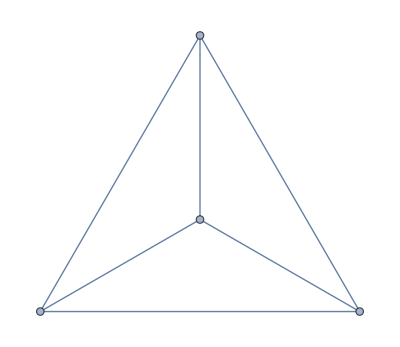

```mathematica
WheelGraph[4]
```

```mathematica
Table[{-x+4+BitShiftRight[x,2]},{x,0,20}]
```

{{4},{3},{2},{1},{1},{0},{-1},{-2},{-2},{-3},{-4},{-5},{-5},{-6},{-7},{-8},{-8},{-9},{-10},{-11},{-11}}

```mathematica
InterpolatingPolynomial[{4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198},n]
```

```mathematica
FullSimplify[4+2 (-1+n)]
```

2 (1+n)

```mathematica
FullSimplify[11+3 (-1+n)]
```

8+3 n

```mathematica
DeleteDuplicates[Sort[Map[Sort,Map[Map[Sort,#]&,Map[pairs,{{0,1,2},{0,1,3,4,2},{0,1,3,5,6,4,2},{0,1,3,5,7,8,6,4,2},{0,1,3,5,7,9,8,6,4,2},{0,2,1},{0,2,4,3,1},{0,2,4,6,5,3,1},{0,2,4,6,8,7,5,3,1},{0,2,4,6,8,9,7,5,3,1},{1,2,4,3},{1,2,4,6,5,3},{1,2,4,6,8,7,5,3},{1,2,4,6,8,9,7,5,3},{1,3,4,2},{1,3,5,6,4,2},{1,3,5,7,8,6,4,2},{1,3,5,7,9,8,6,4,2}}]]]]]//Column
```

{{0,1},{0,2},{1,2}}
{{1,2},{1,3},{2,4},{3,4}}
{{0,1},{0,2},{1,3},{2,4},{3,4}}
{{1,2},{1,3},{2,4},{3,5},{4,6},{5,6}}
{{0,1},{0,2},{1,3},{2,4},{3,5},{4,6},{5,6}}
{{1,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,8}}
{{0,1},{0,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,8}}
{{1,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,9}}
{{0,1},{0,2},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,9}}

```mathematica
{0,1,2,4,5,7,10,8,6,3}+1
```

{1,2,3,5,6,8,11,9,7,4}

```mathematica
Map[{{0,1},{0,2},{1,2},{1,3},{2,4},{3,4},{3,5},{4,6},{5,6},{5,7},{6,8},{7,8},{7,9},{8,9}}[[#]]&,{1,2,3,5,6,8,11,9,7,4}]
```

{{0,1},{0,2},{1,2},{2,4},{3,4},{4,6},{6,8},{5,6},{3,5},{1,3}}

```mathematica
EdgeList[-Graphics-]
```

{0<->1,0<->2,0<->3,0<->4,1<->2,1<->4,2<->3,3<->4}

```mathematica
pairs[list_]:=Table[{list[[1+Mod[i-1,Length[list]]]],list[[1+Mod[i,Length[list]]]]},{i,1,Length[list]}]
```

```mathematica
pairs[{1,2,3,4,5}]
```

{{1,2},{2,3},{3,4},{4,5},{5,1}}

```mathematica
Tally[Sort[Flatten[Map[pairs,ls],1]]]
```

{{{0,1},241},{{0,2},240},{{0,3},319},{{1,0},241},{{1,2},240},{{1,4},319},{{2,0},240},{{2,1},240},{{2,3},161},{{2,4},161},{{3,0},319},{{3,2},161},{{3,5},162},{{3,6},312},{{4,1},319},{{4,2},161},{{4,5},162},{{4,7},312},{{5,3},162},{{5,4},162},{{5,6},162},{{5,7},162},{{6,3},312},{{6,5},162},{{6,8},162},{{6,9},288},{{7,4},312},{{7,5},162},{{7,8},162},{{7,10},288},{{8,6},162},{{8,7},162},{{8,9},162},{{8,10},162},{{9,6},288},{{9,8},162},{{9,11},162},{{9,12},216},{{10,7},288},{{10,8},162},{{10,11},162},{{10,13},216},{{11,9},162},{{11,10},162},{{11,12},162},{{11,13},162},{{12,9},216},{{12,11},162},{{12,13},162},{{13,10},216},{{13,11},162},{{13,12},162}}

```mathematica
375*2
```

750

```mathematica
Map[Length,FindCycle[-Graphics-,∞,All]]
```

{3,3,3,3,4,4,4,4,4,5,5,5,5}

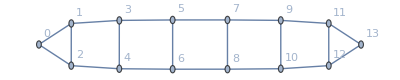

```mathematica
Graph[{0<->1,0<->2,1<->2,11<->13,12<->13,3<->1,4<->2,5<->3,6<->4,7<->5,8<->6,9<->7,10<->8,11<->9,12<->10,3<->4,5<->6,7<->8,9<->10,11<->12},VertexLabels->"Name"]
```

```mathematica
Length[EdgeList[Graph[{0<->1,0<->2,1<->2,11<->13,12<->13,3<->1,4<->2,5<->3,6<->4,7<->5,8<->6,9<->7,10<->8,11<->9,12<->10,3<->4,5<->6,7<->8,9<->10,11<->12}]]]
```

20

```mathematica
Length[FindCycle[Graph[{0<->1,0<->2,1<->2,11<->13,12<->13,3<->1,4<->2,5<->3,6<->4,7<->5,8<->6,9<->7,10<->8,11<->9,12<->10,3<->4,5<->6,7<->8,9<->10,11<->12}],∞,All]]
```

28

```mathematica
Length[FindCycle[Graph[{0<->1,0<->2,1<->2,9<->11,10<->11,3<->1,4<->2,5<->3,6<->4,7<->5,8<->6,9<->7,10<->8,3<->4,5<->6,7<->8,9<->10}],∞,All]]
```

21

```mathematica
FindCycle[Graph[{0<->1,0<->2,1<->2,9<->11,10<->11,3<->1,4<->2,5<->3,6<->4,7<->5,8<->6,9<->7,10<->8,3<->4,5<->6,7<->8,9<->10}],∞,All]
```

{{9<->11,11<->10,10<->9},{0<->1,1<->2,2<->0},{6<->5,5<->7,7<->8,8<->6},{3<->5,5<->6,6<->4,4<->3},{9<->10,10<->8,8<->7,7<->9},{1<->3,3<->4,4<->2,2<->1},{9<->11,11<->10,10<->8,8<->7,7<->9},{0<->1,1<->3,3<->4,4<->2,2<->0},{3<->5,5<->7,7<->8,8<->6,6<->4,4<->3},{9<->10,10<->8,8<->6,6<->5,5<->7,7<->9},{1<->3,3<->5,5<->6,6<->4,4<->2,2<->1},{9<->11,11<->10,10<->8,8<->6,6<->5,5<->7,7<->9},{0<->1,1<->3,3<->5,5<->6,6<->4,4<->2,2<->0},{9<->10,10<->8,8<->6,6<->4,4<->3,3<->5,5<->7,7<->9},{1<->3,3<->5,5<->7,7<->8,8<->6,6<->4,4<->2,2<->1},{9<->11,11<->10,10<->8,8<->6,6<->4,4<->3,3<->5,5<->7,7<->9},{0<->1,1<->3,3<->5,5<->7,7<->8,8<->6,6<->4,4<->2,2<->0},{1<->3,3<->5,5<->7,7<->9,9<->10,10<->8,8<->6,6<->4,4<->2,2<->1},{1<->3,3<->5,5<->7,7<->9,9<->11,11<->10,10<->8,8<->6,6<->4,4<->2,2<->1},{0<->1,1<->3,3<->5,5<->7,7<->9,9<->10,10<->8,8<->6,6<->4,4<->2,2<->0},{0<->1,1<->3,3<->5,5<->7,7<->9,9<->11,11<->10,10<->8,8<->6,6<->4,4<->2,2<->0}}

```mathematica
pairs[{1,2,3,4,5}]
```

{{1,2},{2,3},{3,4},{4,5},{5,1}}